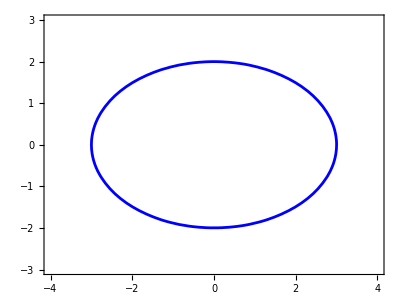

```mathematica
ContourPlot[4x^2+9y^2==36,{x,-4,4},{y,-3,3},AspectRatio->Automatic,ContourStyle->Directive[Blue,Thickness[0.005]]]
```

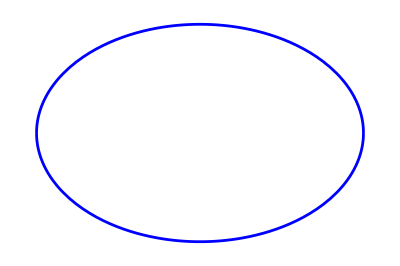

```mathematica
Plot[{2*Sqrt[1-x^2/9],-2*Sqrt[1-x^2/9]},{x,-3,3},AspectRatio->Automatic,PlotStyle->Directive[Blue,Thickness[0.005]],Axes->False]
```

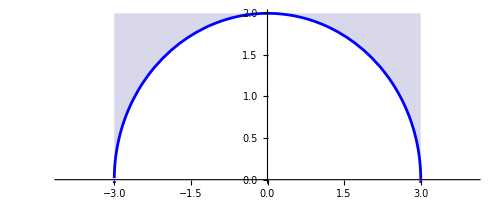

```mathematica
f1=Plot[2*Sqrt[1-x^2/9],{x,-4,4},AspectRatio->Automatic,PlotStyle->Directive[Blue,Thickness[0.005]],Filling->Top];
f2=Plot[-2*Sqrt[1-x^2/9],{x,-4,4},AspectRatio->Automatic,PlotStyle->Directive[Blue,Thickness[0.005]],Filling->Bottom];
Show[f1,f2]
```

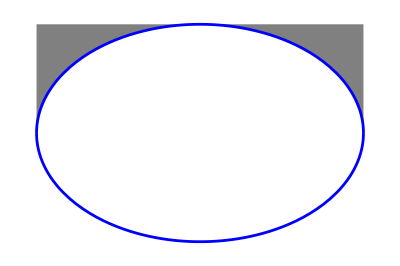

```mathematica
Plot[{2*Sqrt[1-x^2/9],-2*Sqrt[1-x^2/9]},{x,-3,3},AspectRatio->Automatic,PlotStyle->Directive[Blue,Thickness[0.005]],Axes->False,Filling->{1->{2,Gray}}]
```

```mathematica
Manipulate[ContourPlot[{(x-5/3(Cos[t])^3)^2+(y+2.5(Sin[t])^3)^2==(4+5(Sin[t])^2)^3/36,4x^2+9y^2==36,(x-3Cos[t])^2+(y-2Sin[t])^2==0.005},{x,-5,5},{y,-5,5},AspectRatio->Automatic,ContourStyle->{Directive[Red,Thickness[0.003]],Directive[Blue,Thickness[0.008]],Directive[Red,Thickness[0.01]]}],{t,0,2Pi}]
```

```mathematica
Manipulate[ContourPlot[{(x-5/3Cos[t])^2+(y-2/3Sin[t])^2==16/9,4x^2+9y^2==36,(x-3Cos[t])^2+(y-2Sin[t])^2==0.005},{x,-4,4},{y,-3,3},AspectRatio->Automatic,ContourStyle->{Directive[Red,Thickness[0.003]],Directive[Blue,Thickness[0.008]],Directive[Red,Thickness[0.01]]}],{t,0,2Pi}]
```